```mathematica
ClearAll["Global`*"]
```

### Basis for Relevant Polynomial Spaces

```mathematica
SetDirectory[NotebookDirectory[]];
pascalLine[i_]:= Table[x^j y^(i-j),{j,0,i}];
PkBasis[x_,k_]:=Table[x^j,{j,0,k}];
PkXYBasis[i_]:=Flatten[Table[pascalLine[j],{j,0,i}]];
PkXYTildeBasis[i_]:=pascalLine[i];
SkBasis[k_]:=Table[PkXYTildeBasis[k-1][[j]]{y,-x},{j,1,Length[PkXYTildeBasis[k-1]]}];
Pk2Basis[k_]:=Flatten[Join[Table[
Join[Table[{PkXYTildeBasis[i][[j]],0},{j,1,Length[PkXYTildeBasis[i]]}],Table[{0,PkXYTildeBasis[i][[j]]},{j,1,Length[PkXYTildeBasis[i]]}]],{i,0,k}]],1];
PkTilde2Basis[k_]:=
Join[Table[{PkXYTildeBasis[k][[j]],0},{j,1,Length[PkXYTildeBasis[k]]}],Table[{0,PkXYTildeBasis[k][[j]]},{j,1,Length[PkXYTildeBasis[k]]}]];
RkBasis[k_]:=Join[SkBasis[k],Pk2Basis[k-1]];
NotebookDirectory[]
```

/Users/Orlandini/Documents/UNICAMP/Labmec/Mathematica/HCurl/Triangle/

### Calculate Basis Functions for Triangular Element

```mathematica
CalcFuncs[k_,tDeformed_,elDeformed_,c_]:=Block[{t,refEl,ϕVec,nEdges,nEdgeDof,nInternalDof,nFuncPerEdge,edgeIndex,pkIndex,ϕVecOld,nEdgeDofOld,nInternalDofOld,nFuncPerEdgeOld,edgeIndexOld,ϕVecNew,nEdgeDofNew,nInternalDofNew,basisFuncs,basisFuncsOld,nBasisFuncs,dcds,s,mat,i,j,x,y,l,ϕIndex,rhs,α,ϕ, nOldFuncs,pkVec, pk2Vec},
t={{1,0},1/(√2){-1,1},{0,-1}};
refEl=Triangle[{{0,0},{1,0},{0,1}}];
ϕVec={};
basisFuncs={};
nEdges=Length[t];
nFuncPerEdge=k;
nEdgeDof= nEdges* nFuncPerEdge;
nInternalDof = k(k-1);
edgeIndex=Table[Quotient[i,k,-(k-1)],{i,1,nEdgeDof}];
If[k>0,
{ϕVecOld,nEdgeDofOld,nInternalDofOld,nFuncPerEdgeOld,edgeIndexOld, basisFuncsOld}=CalcFuncs[k-1,t,refEl,c];
nEdgeDofNew=nEdges;
nInternalDofNew=Length[PkTilde2Basis[k-2]];
basisFuncs=Join[basisFuncsOld,Grad[PkXYTildeBasis[k],{x,y}],SkBasis[k]];
nBasisFuncs=Length[basisFuncs];
dcds[s_]:=D[c[s],s];
ϕVecNew={};
pk2Vec=Pk2Basis[k-2];
pkVec=PkBasis[s,k-1];
pkIndex=Table[Mod[i,Length[pkVec],1],{i,1,nEdgeDof}];
nOldFuncs=nInternalDofOld+nEdgeDofOld;
mat=Table[0,{i,1,nBasisFuncs},{j,1,nBasisFuncs}];
Print["k = ", k, " nDofNew = ", nBasisFuncs," nAdditionalFuncs = ", nOldFuncs];
For[i=1,i≤ nEdgeDof,i++,
For[j=1,j≤ nBasisFuncs,j++,
mat[[i,j]]=Integrate[((t[[edgeIndex[[i]]]].basisFuncs[[j]])/.{x-> c[s][[edgeIndex[[i]],1]],y-> c[s][[edgeIndex[[i]],2]]})*pkVec[[pkIndex[[i]]]]*√((dcds[s][[edgeIndex[[i]],1]])^2+(dcds[s][[edgeIndex[[i]],2]])^2),{s,0,1}];
];
];
For[i=1,i≤ nInternalDof,i++,
For[j=1,j≤ nBasisFuncs,j++,
mat[[nEdgeDof+i,j]]=Integrate[basisFuncs[[j]].pk2Vec[[i]],{x,y}∈refEl];
];
];
For[i=1,i≤ nEdges,i++,
rhs=Table[0,{i,1, nBasisFuncs}];
rhs[[(i-1)*nFuncPerEdge+nFuncPerEdgeOld+1]]=1;
α=LinearSolve[mat,rhs];
ϕ=Sum[(basisFuncs*α)[[i]],{i,1,nBasisFuncs}];
AppendTo[ϕVecNew,ϕ];
];
For[ϕIndex=1,ϕIndex≤ nInternalDofNew,ϕIndex++,
rhs=Table[0,{i,1, nBasisFuncs}];
rhs[[nEdgeDof+nInternalDofOld+ϕIndex]]=1;
α=LinearSolve[mat,rhs];
ϕ=Sum[(basisFuncs*α)[[i]],{i,1,nBasisFuncs}];
AppendTo[ϕVecNew,ϕ];
];
ϕVec={};
For[i=1,i≤ nEdges,i++,
For[j=1,j≤ nFuncPerEdgeOld,j++,AppendTo[ϕVec,ϕVecOld[[nFuncPerEdgeOld*(i-1)+j]] ]];
AppendTo[ϕVec,ϕVecNew[[i]] ];
];

For[i=1,i≤ nInternalDofOld,i++,AppendTo[ϕVec,ϕVecOld[[nFuncPerEdgeOld*nEdges+i]]]];
For[i=1,i≤ nInternalDofNew,i++,AppendTo[ϕVec,ϕVecNew[[nEdgeDofNew+i]]]];
];
{ϕVec,nEdgeDof,nInternalDof,nFuncPerEdge,edgeIndex,basisFuncs}
];
```

### Define Reference Triangular Element

```mathematica
t={{1,0},1/(√2){-1,1},{0,-1}};
refEl=Triangle[{{0,0},{1,0},{0,1}}];
parametricEdges[s_]:={{s,0},{1-s,s},{0,1-s}};
```

### Get Basis Functions

```mathematica
kPoly = 15;
genScaled = True;
printEdge = True;
printInternal = False;
{ϕVecH,nEdgeDof,nInternalDof,nFuncPerEdge,edgeId,basisFuncs}=CalcFuncs[kPoly,t,refEl,parametricEdges];
ϕEdgesH=Table[ϕVecH[[i]],{i,1,nEdgeDof}];
ϕInternalH=Table[ϕVecH[[i]],{i,nEdgeDof+1,nEdgeDof+nInternalDof}];
Length[ϕVecH]
If[genScaled==True,
ϕEdgesH=Table[ϕEdgesH[[i]]/(ϕEdgesH[[i]].t[[edgeId[[i]]]]/.{x-> parametricEdges[qsi][[edgeId[[i]],1]],y-> parametricEdges[qsi][[edgeId[[i]],2]]})/.{qsi-> 1},{i,1,Length[ϕEdgesH]}];
ϕInternalH=Table[ϕInternalH[[i]]/NMaxValue[{Norm[ϕInternalH[[i]]],{x,y}∈refEl},{x,y}],{i,1,Length[ϕInternalH]}];
];
```

k = 1 nDofNew = 3 nAdditionalFuncs = 0

k = 2 nDofNew = 8 nAdditionalFuncs = 3

k = 3 nDofNew = 15 nAdditionalFuncs = 8

k = 4 nDofNew = 24 nAdditionalFuncs = 15

k = 5 nDofNew = 35 nAdditionalFuncs = 24

k = 6 nDofNew = 48 nAdditionalFuncs = 35

k = 7 nDofNew = 63 nAdditionalFuncs = 48

k = 8 nDofNew = 80 nAdditionalFuncs = 63

k = 9 nDofNew = 99 nAdditionalFuncs = 80

k = 10 nDofNew = 120 nAdditionalFuncs = 99

k = 11 nDofNew = 143 nAdditionalFuncs = 120

k = 12 nDofNew = 168 nAdditionalFuncs = 143

k = 13 nDofNew = 195 nAdditionalFuncs = 168

k = 14 nDofNew = 224 nAdditionalFuncs = 195

k = 15 nDofNew = 255 nAdditionalFuncs = 224

255

### Analysis of Tangential Traces (Edge Functions)

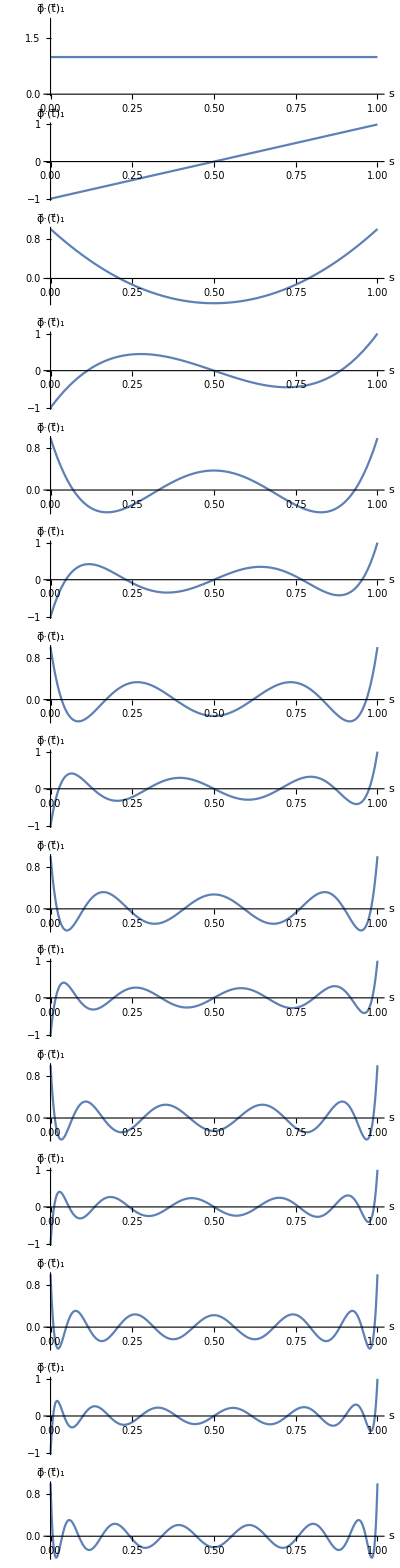

```mathematica
If[printEdge==True,
ϕBound=Table[
ϕEdgesH[[i]].t[[edgeId[[i]]]]/.{x-> parametricEdges[s][[edgeId[[i]],1]],y-> parametricEdges[s][[edgeId[[i]],2]]},{i,1,Length[ϕEdgesH]}];
funcAnalysisTableEdge=Table[
{Plot[ϕBound[[i]],{s,0,1},ImageSize->Medium,AxesLabel->{"s","ϕ⃗·(t⃗)_1"}]
},{i,1,nFuncPerEdge}];
Print[Grid[funcAnalysisTableEdge]];
];
```

### Analysis of Tangential Traces (Internal Functions)

```mathematica
If[printInternal==True,
funcAnalysisTableEdge2=Table[
{
VectorPlot[ϕInternalH[[i]],{x,y}∈ refEl,ImageSize->Medium,VectorPoints-> 10],Plot[(ϕInternalH[[i]].t[[1]])/.{x-> parametricEdges[s][[1,1]],y-> parametricEdges[s][[1,2]]},{s,0,1},ImageSize->Medium,AxesLabel->{"s","ϕ⃗·(t⃗)_1"}],
Plot[(ϕInternalH[[i]].t[[2]])/.{x-> parametricEdges[s][[2,1]],y-> parametricEdges[s][[2,2]]},{s,0,1},ImageSize->Medium,AxesLabel->{"s","ϕ⃗·(t⃗)_2"}],
Plot[(ϕInternalH[[i]].t[[3]])/.{x-> parametricEdges[s][[3,1]],y-> parametricEdges[s][[3,2]]},{s,0,1},ImageSize->Medium,AxesLabel->{"s","ϕ⃗·(t⃗)_3"}]
},{i,1,Length[ϕInternalH]}];
Print[Grid[funcAnalysisTableEdge2]];
];
```

### Generate C Form Edge Functions

```mathematica
For[ i = 1 , i≤ 3 , i++,
out={};
For[j = nFuncPerEdge, j> 0 , j--,
out=StringJoin[out,StringJoin["case ",ToString[j],":\n",
"\tphi( currentFuncPos , 0 ) = ",ToString[CForm[Simplify[ϕEdgesH[[nFuncPerEdge*(i-1)+j,1]]]]],";\n" ,
"\tphi( currentFuncPos , 1 ) = ",ToString[CForm[Simplify[ϕEdgesH[[nFuncPerEdge*(i-1)+j,2]]]]],";\n",
"\tcurlPhiHat( 0 , currentFuncPos ) = ",ToString[CForm[Simplify[Curl[ϕEdgesH[[nFuncPerEdge*(i-1)+j]],{x,y}]]]],";\n"]];
If[j==1, out=StringJoin[out,"\tbreak;\n"],out = StringJoin[out,"\tcurrentFuncPos --;\n"]];
];
If[genScaled==True,
Export["funcScaledEdge"<>ToString[i-1]<>".txt",out];
,
Export["funcEdge"<>ToString[i-1]<>".txt",out];
];
];
```

### Generate C Form Internal Functions

```mathematica
out={};
currentPos = Length[ϕInternalH];
funcCount = 0;
Print["Printed ",Dynamic[funcCount]," internal functions."];
For[ k = kPoly , k≥ 2 , k--,
nFuncPerK = 2*(k-1);
out=StringJoin[out,"case ",ToString[k],":\n"];
For[j = 0, j<nFuncPerK,j++,
out=StringJoin[out,StringJoin[
"\tphi( currentFuncPos , 0 ) = ",ToString[CForm[Simplify[ϕInternalH[[currentPos,1]]]]],";\n" ,
"\tphi( currentFuncPos , 1 ) = ",ToString[CForm[Simplify[ϕInternalH[[currentPos,2]]]]],";\n",
"\tcurlPhiHat( 0 , currentFuncPos ) = ",ToString[CForm[Simplify[Curl[ϕInternalH[[currentPos]],{x,y}]]]],";\n"]
];
currentPos--;
funcCount++;
If[j== nFuncPerK - 1&& k ==2, out=StringJoin[out,"\tbreak;\n"],out = StringJoin[out,"\tcurrentFuncPos --;\n"]];
];
];
If[genScaled==True,
Export["funcScaledInternal.txt",out];
,
Export["funcInternal.txt",out];
];
```

Printed  internal functions.

### Generate C Form Edge Functions @ Edges (Boundary Elements)

```mathematica
ϕBound=Table[
ϕEdgesH[[i]].t[[edgeId[[i]]]]/.{x-> parametricEdges[qsi[0]][[edgeId[[i]],1]],y-> parametricEdges[qsi[0]][[edgeId[[i]],2]]},{i,1,nFuncPerEdge}];
out={};
For[j = nFuncPerEdge, j> 0 , j--,
out=StringJoin[out,StringJoin["case ",ToString[j],":\n",
"\tphi( currentFuncPos , 0 ) = ",ToString[CForm[Simplify[ϕBound[[j]]]]],";\n" ]];
If[j==1, out=StringJoin[out,"\tbreak;\n"],out = StringJoin[out,"\tcurrentFuncPos --;\n"]];
];
If[genScaled==True,
Export["funcScaledEdgeBound.txt",out];
,
Export["funcEdgeBound.txt",out];
];
```